```mathematica
3*4
```

12

```mathematica
FactorInteger[12]
```

{{2,2},{3,1}}

```mathematica
Max[First/@{{2,2},{3,1}}]
```

3

```mathematica
5/3
```

5/3

```mathematica
N[5/3]
```

1.66667

```mathematica
N[pi, 10000]
```

pi

```mathematica
N[pi, 100]
```

pi

```mathematica
N[Pi, 100]
```

3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117068

```mathematica
5.0/3
```

1.66667

```mathematica
Hold[a/b]
```

Hold[a/b]

```mathematica
xy
```

xy

```mathematica
x
```

x

```mathematica
y
```

y

```mathematica
x*y
```

x y

Cos[x]^2+Sin[x]^2

```mathematica
Simplify[Sin[x]^2 + Cos[x]^2]
```

1

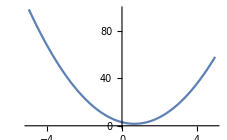

```mathematica
Plot[3.x^2 - 4.*x+3, {x, -5, 5}]
```

```mathematica
term1
23
```

term1

23

```mathematica
clear[x]
```

clear[x]

```mathematica
term1
```

term1

```mathematica
term1 = 8 - x^2 + x^3
```

8-x^2+x^3

```mathematica
term1
```

8-x^2+x^3

```mathematica
term2 = D[term1, x]
```

-2 x+3 x^2

```mathematica
term3 = Integrate[term1, x]
```

8 x-x^3/3+x^4/4

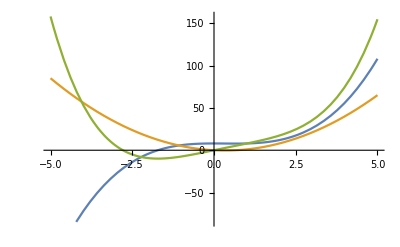

```mathematica
Plot[{term1, term2, term3}, {x, -5, 5}]
```

```mathematica
?Plot
```

Plot[f,{x,x_min,x_max}] generates a plot of f as a function of x from x_min to x_max. 
Plot[{f_1,f_2,…},{x,x_min,x_max}] plots several functions f_i. 
Plot[{…,w[f_i],…},…] plots f_i with features defined by the symbolic wrapper w.
Plot[…,{x}∈reg] takes the variable x to be in the geometric region reg.

```mathematica
Options[Plot]
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,Exclusions→Automatic,ExclusionsStyle→None,Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},MaxRecursion→Automatic,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLabels→None,PlotLegends→None,PlotPoints→Automatic,PlotRange→{Full,Automatic},PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,ScalingFunctions→None,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{},WorkingPrecision→MachinePrecision}

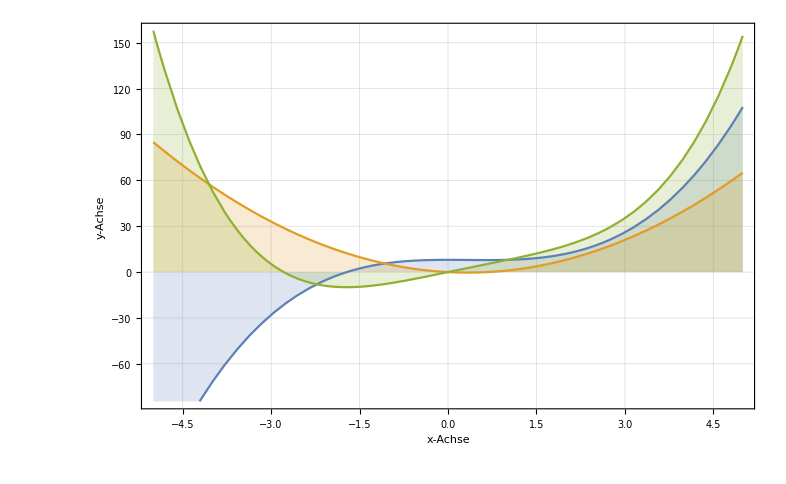

```mathematica
Plot[{term1, term2, term3}, {x, -5, 5}, Frame -> True, Filling -> Axis, GridLines -> Automatic, FrameLabel -> {"x-Achse", "y-Achse"}]
```

```mathematica
mystyle =  {Frame -> True, Filling -> Axis, GridLines -> Automatic, FrameLabel -> {"x-Achse", "y-Achse"}}
```

{Frame→True,Filling→Axis,GridLines→Automatic,FrameLabel→{x-Achse,y-Achse}}

```mathematica
Plot[term1, {x, -10, 10}, mystyle]
```

Plot::nonopt: Options expected (instead of mystyle) beyond position 2 in Plot[term1,{x,-10,10},mystyle]. An option must be a rule or a list of rules.

Plot[term1,{x,-10,10},mystyle]

```mathematica
mystyle2 = Frame -> True, Filling -> Axis, GridLines -> Automatic, FrameLabel -> {"x-Achse", "y-Achse"}
```

```mathematica
Plot[term1, {x, -10, 10}, mystyle2]
```

Plot::nonopt: Options expected (instead of mystyle2) beyond position 2 in Plot[term1,{x,-10,10},mystyle2]. An option must be a rule or a list of rules.

Plot[term1,{x,-10,10},mystyle2]

```mathematica
va = {1,2,3}
```

{1,2,3}

```mathematica
vb = {a,b,c}
```

{a,b,c}

```mathematica
3*vb
```

{3 a,3 b,3 c}

```mathematica
vb * va
```

{a,2 b,3 c}

```mathematica
va . vb
```

a+2 b+3 c

```mathematica
FullForm[a+b+c]
```

Plus[a,b,c]

```mathematica
Apply[Plus, vb]
```

a+b+c

```mathematica
mat = {{a,b,c},{d,e,f}}
```

{{a,b,c},{d,e,f}}

```mathematica
MatrixForm[mat]
```

(a | b | c
d | e | f)

```mathematica
FullForm[mat]
```

List[List[a,b,c],List[d,e,f]]

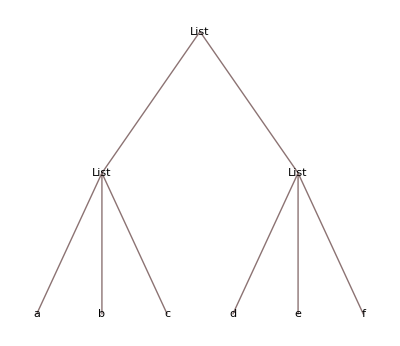

```mathematica
TreeForm[mat]
```

```mathematica
Apply[Plus, mat]
```

gibt die Summe über die Spalten

{a+d,b+e,c+f}

```mathematica
Apply[Plus, mat, {1}]
```

{rekursive} Summe über die Zeilen, 1 bezieht sich auf das Level im Baum

{a+b+c,d+e+f}

Doppelt eckige Klammern haben Bedeutung des Elementzugriffs:

```mathematica
mat[[2]]
```

{d,e,f}

```mathematica
mat[[All,2]]
```

{b,e}

```mathematica
?;;
```

i;;j represents a span of elements i through j.
i;; represents a span from i to the end.
;;j represents a span from the beginning to j.
;; represents a span that includes all elements.
i;;j;;k represents a span from i through j in steps of k.
i;;;;k represents a span from i to the end in steps of k.
;;j;;k represents a span from the beginning to j in steps of k.
;;;;k represents a span from the beginning to the end in steps of k.

```mathematica
mat[[1;;-1, 2]]
```

{b,e}

```mathematica
mat[[1;;2, 2;;3]]
```

{{b,c},{e,f}}

```mathematica
Det[mat[[1;;2, 2;;3]]]
```

-c e+b f

Zweiter Tag

```mathematica
ag1 = 3-5*t
```

```mathematica
3-5 t
```

3-5 t

Lokale Ersetzungen vonVariablen

```mathematica
ag1 /.t -> 3.
```

```mathematica
-12.
```

Funktionen definieren: 
- Alle Variablen mit _ sind Platzhalter
- := ist tag-delay, Auführung erst wenn Argument gegeben wird

```mathematica
myfun[t_]:= 2*t^2 + 3*t
```

```mathematica
myfun[3]
```

27

```mathematica
D[myfun[x], x]
```

3+4 x

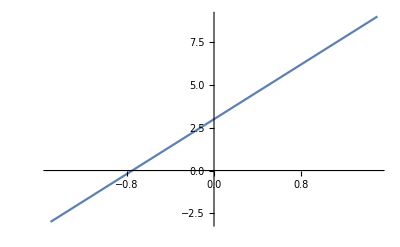

```mathematica
Plot[3+4 x,{x,-1.5,1.5}]
```

```mathematica
parabel[a_, b_, c_, t_] := a * t^2 + b*t + c
```

```mathematica
parabel[1.,2.,3.,4.]
```

27.

```mathematica
myfun[2.,]
```

myfun[2.,Null]

```mathematica
myfun[2.]
```

14.

```mathematica
FullForm[myfun]
```

myfun

```mathematica
fun1 = Function[{x}, 3*x^2]
```

Function[{x},3 x^2]

```mathematica
fun1[1.]
```

```mathematica
3.
```

3.

```mathematica
fun2 = 3. * #1^2 + #2^3&
```

3. #1^2+#2^3&

```mathematica
fun2[1,2]
```

11.

```mathematica
fun1c = Compile [{x}, 3*x^2]
```

CompiledFunction[…]

```mathematica
mat = {{a,b,c},{d,e,f}}
```

{{a,b,c},{d,e,f}}

```mathematica
MatrixForm[mat]
```

(a | b | c
d | e | f)

```mathematica
funq[x_]:= x^2
```

```mathematica
Map[func, mat, {2}]
```

{{func[a],func[b],func[c]},{func[d],func[e],func[f]}}

```mathematica
Map[funq, mat, {2}]
```

{{a^2,b^2,c^2},{d^2,e^2,f^2}}

```mathematica
fun10 [x_] := {x[[1]], x[[2]]^2, Sqrt[x[[3]]]}
```

```mathematica
MatrixForm[Map[fun10, mat, {1}]]
```

(a | b^2 | √c
d | e^2 | √f)

```mathematica
fun11[x_, y_, z_] := {x, y^2, Sqrt[z]}
```

```mathematica
MatrixForm[Apply[fun11, mat, {1}]]
```

(a | b^2 | √c
d | e^2 | √f)

```mathematica
Directory[]
```

/afs/urz.uni-heidelberg.de/usr/fphys/wo443

```mathematica
FileNames[]
```

{.adobe,.allread,.bash_history,Bilder,.cache,.claws-mail,coll.m,.config,.dbus,Dokumente,Downloads,dummy.m,.gconf,.gnome,.gnome2,.gnome2_private,.gstreamer-0.10,.ICEauthority,.ipynb_checkpoints,.ipython,.jupyter,.kde,.local,.macromedia,Mail,.Mathematica,mathematica,.matlab,.mozilla,Musik,Öffentlich,.pki,.plan,plotSinus.m,.profile,.pulse-cookie,Schreibtisch,.ssh,sum.m,summe.m,Videos,Vorlagen,.Wolfram,.Wolfram Research,.x2go,.Xauthority,.xsession-errors}

```mathematica
SetDirectory["/afs/urz.uni-heidelberg.de/usr/fphys/wo443/mathematica/Data"]
```

/afs/urz.uni-heidelberg.de/usr/fphys/wo443/mathematica/Data

```mathematica
FileNames["*.dat"]
```

{Rdat2.dat,Rdat3.dat}

```mathematica
data = Import["Rdat3.dat", "Table"];
```

```mathematica
data
```

{{0.,9975},{1.,8934},{2.,8094},{3.,7179},{4.,6478},{5.,5805},{6.,5271},{7.,4537},{8.,4051},{9.,3705},{10.,3263},{11.,2959},{12.,2626},{13.,2420},{14.,2179},{15.,1938},{16.,1756},{17.,1512},{18.,1374},{19.,1238},{20.,1079},{21.,985},{22.,861},{23.,747},{24.,649},{25.,605},{26.,561},{27.,502},{28.,431},{29.,395},{30.,362}}

```mathematica
Dimensions[data]
```

{31,2}

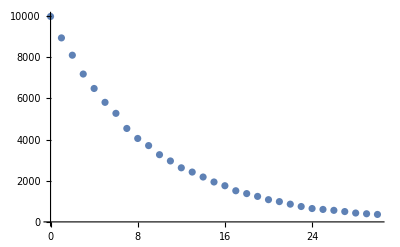

```mathematica
ListPlot[data]
```

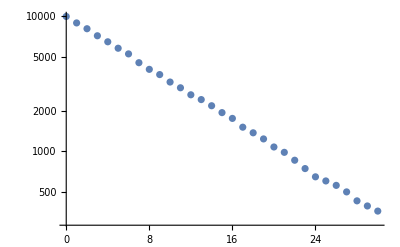

```mathematica
ListLogPlot[data]
```

```mathematica
?Hold
```

Hold[expr] maintains expr in an unevaluated form.

```mathematica
?Clear
```

Clear[symbol_1,symbol_2,…] clears values and definitions for the symbol_i. 
Clear[form,form,…] clears values and definitions for all symbols whose names match any of the string patterns form_i.

```mathematica
?Tally
```

Tally[list] tallies the elements in list, listing all distinct elements together with their multiplicities.
Tally[list,test] uses test to determine whether pairs of elements should be considered equivalent, and gives a list of the first representatives of each equivalence class, together with their multiplicities.

```mathematica
?BarChart
```

BarChart[{y_1,y_2,…}] makes a bar chart with bar lengths y_1,  y_2, ….
BarChart[{…,w_i[y_i,…],…,w_j[y_j,…],…}] makes a bar chart with bar features defined by the symbolic wrappers w_k.
BarChart[{data_1,data_2,…}] makes a bar chart from multiple datasets data_i.

```mathematica
?Depth
```

Depth[expr] gives the maximum number of indices needed to specify any part of expr, plus 1.

```mathematica
SetDirectory["/afs/urz.uni-heidelberg.de/usr/fphys/wo443/mathematica/data"]
```

/afs/urz.uni-heidelberg.de/usr/fphys/wo443/mathematica/data

```mathematica
Directory[]
```

/afs/urz.uni-heidelberg.de/usr/fphys/wo443/mathematica/data

```mathematica
FileNames[]
```

{iudata.asc,Myplotfun.asc,Rdat2.dat,Rdat3.dat}

```mathematica
data1 = Import["iudata.asc"]
```

{{1.,23.},{2.,42.},{3.,64.},{4.,85.},{5.,106.},{6.,121.},{7.,154.},{8.,159.},{9.,189.},{10.,195.}}

```mathematica
data = Apply[{#1,#2,4.+ 0.02*#2}&,data1,{1}]
```

{{1.,23.,4.46},{2.,42.,4.84},{3.,64.,5.28},{4.,85.,5.7},{5.,106.,6.12},{6.,121.,6.42},{7.,154.,7.08},{8.,159.,7.18},{9.,189.,7.78},{10.,195.,7.9}}

```mathematica
Get["Myplotfun.asc"]
```

```mathematica
plot1 = MyPlotfun[data,Frame -> True,GridLines -> Automatic,FrameLabel -> {"U [V]","I [mA]"}]
```

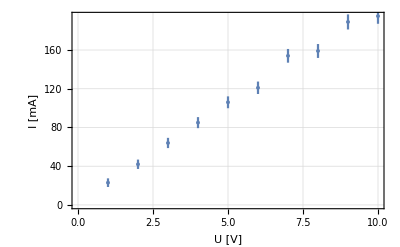

-Graphics-

```mathematica
fitfun = a*x + b
```

b+a x

```mathematica
fiterg = MyFit[data, fitfun, {{a, 20.}, {b, 0.}}]
```

FittedModel[3.65906+20.0104 x]

```mathematica
GetFitpar[fiterg]
```

{{8,0.592866,0.215334},{a,20.0104,0.672343},{b,3.65906,3.51876}}

```mathematica
Get["Myplotfun.asc"]
```

```mathematica
data = Import["Sin1_f1_m2.tab", "Table"][[2;;-1]];
```

```mathematica
Length[data]
```

2046

```mathematica
Dimensions[data]
```

{2046,3}

Annahme: Fehler der Daten ist Auflösung

```mathematica
yerr = 0.8/256
```

```mathematica
0.003125
```

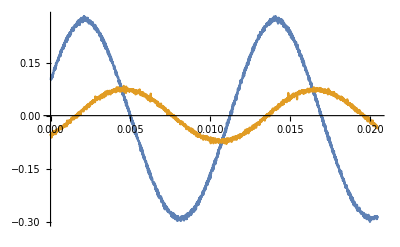

```mathematica
plot1 = ListLinePlot[{data[[All, {1,2}]],data[[All, {1,3}]]}]
```

```mathematica
can1 = Apply[{#1, #2, yerr}&, data, {1}];
can2 = Apply[{#1, #3, yerr}&, data, {1}];
```

```mathematica
can1fit01 = MyFit[can1, acos * Cos[om*x] + asin * Sin[om *x] + u0, {{acos, .1}, {asin, .1}, {u0, 0.}, {om,500.}}]
```

FittedModel[-0.014707+«20» Cos[«18» x]+0.250097 Sin[525.941 x]]

Fitfunktion[daten, fitfunktion, Liste von Parametern mit {Parameter, Startwert}]

```mathematica
GetFitpar[can1fit01]
```

{{2042,3.54127,0.},{acos,0.119908,0.000369044},{asin,0.250097,0.000239833},{u0,-0.014707,0.000135149},{om,525.941,0.125029}}

```mathematica
?MyFit
```

Global`MyFit

MyFit[data_,fitfun_,partab_,invar_:x]:=NonlinearModelFit[data⟦All,1;;2⟧,fitfun,partab,invar,Weights→(1/#1^2&)/@data⟦All,3⟧]

```mathematica
?GetFitpar
```

Global`GetFitpar

GetFitpar[fiterg_]:=Module[{chisq=fiterg[ANOVATableEntries]⟦2,-1⟧,dof=fiterg[ANOVATableEntries]⟦2,1⟧,proval,partab=fiterg[ParameterTable]⟦1,1,2;;-1,1;;3⟧},proval=If[chisq>1,1.-CDF[ChiSquareDistribution[dof],dof chisq],CDF[ChiSquareDistribution[dof],dof chisq]];Prepend[If[proval<0.05,partab,Apply[{#1,#2,#3/(√chisq)}&,partab,{1}]],{dof,chisq,proval}]]

```mathematica
can2fit01 = MyFit[can2, acos * Cos[om*x] + asin * Sin[om *x] + u0, {{acos, .1}, {asin, .1}, {u0, 0.}, {om,500.}}]
```

FittedModel[0.00120085-«20» Cos[«1»]+0.0475317 Sin[526.077 x]]

```mathematica
GetFitpar[can2fit01]
```

{{2042,0.974944,0.212737},{acos,-0.0550025,0.000140207},{asin,0.0475317,0.000159567},{u0,0.00120085,0.0000743769},{om,526.077,0.21328}}

```mathematica
plot2 = Plot[{Evaluate[can1fit01["BestFit"]], Evaluate[can2fit01["BestFit"]]}]
```

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

```mathematica
Plot[ {Evaluate[can1fit01["BestFit"]],Evaluate[can2fit01["BestFit"]]}]
```

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

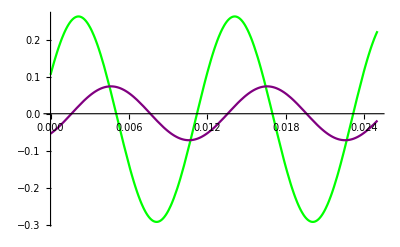

```mathematica
Plot[{Evaluate[can1fit01["BestFit"]],Evaluate[can2fit01["BestFit"]]}, {x, 0, .025}, PlotStyle -> {Green, Purple}]
```

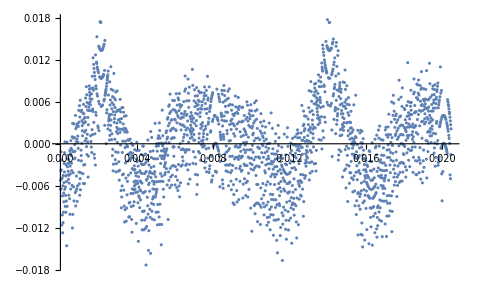

```mathematica
ListPlot[Apply[Evaluate[{#1, #2 - GetBestFit[can1fit01][#1]}]&, data[[All, {1,2}]], {1}]]
```

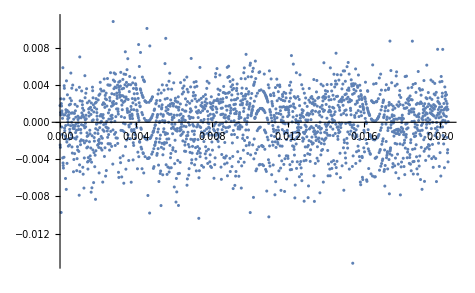

```mathematica
ListPlot[Apply[Evaluate[{#1, #2 - GetBestFit[can2fit01][#1]}]&, data[[All, {1,3}]], {1}]]
```

```mathematica
datag = Join[Apply[{{#1, 1}, #2, yerr}&, data, {1}], Apply[{{#1, 1}, #3, yerr}&, data, {1}]];
```

```mathematica
gfit01=MyFitmd[datag, Which[can ==1, a1cos*Cos[om*x]+a1sin*Sin[om*x]+u01, 
can ==2, a2cos*Cos[om*x]+a2sin*Sin[om*x]+u02],{{a1cos, .1}, {a1sin, .1},{a2cos,.1},{a2sin,.1},{om, 500.}, {u01,0.}, {u02, 0.}}, {x,can}]
```

FittedModel[Which[can==1,0.0324555 Cos[525.96 x]+«19» Sin[«1»]-0.00675758,«1»,0.1 Cos[525.96 x]+0.1 Sin[525.96 x]+0.]]

```mathematica
GetFitpar[gfit01]
```

{{4085,997.149,0.},{a1cos,0.0324555,0.00445043},{a1sin,0.14886,0.00237489},{a2cos,0.1,1.69313×10^-17},{a2sin,0.1,0.},{om,525.96,2.56005},{u01,-0.00675758,0.00162363},{u02,0.,0.}}

```mathematica
gfit01["CorrelationMatrix"]
```

FittedModel::zerocov: CorrelationMatrix cannot be computed in the case of zero elements on the diagonal of "CovarianceMatrix".

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

{{1.,-0.330755,0.870619,Indeterminate,-0.870618,-0.131943,Indeterminate},{-0.330755,1.,-0.320563,Indeterminate,0.320563,-0.0895755,Indeterminate},{0.870619,-0.320563,1.,Indeterminate,-1.,-0.230155,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{-0.870618,0.320563,-1.,Indeterminate,1.,0.230155,Indeterminate},{-0.131943,-0.0895755,-0.230155,Indeterminate,0.230155,1.,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate}}

```mathematica
MyErrorPropagation[gfit01, Sqrt[a1cos^2+a1sin^2]]
```

FittedModel::zerocov: CorrelationMatrix cannot be computed in the case of zero elements on the diagonal of "CovarianceMatrix".

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

{0.152357,Indeterminate}

```mathematica
g = Graph[{1,2,3,4,5,6}]
```

Graph[{1,2,3,4,5,6}]

```mathematica
FullForm[g]
```

Graph[List[1,2,3,4,5,6]]

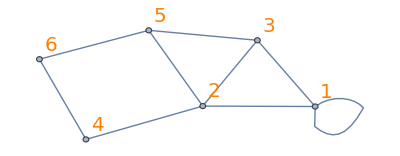

```mathematica
g1 = Graph[{1<->2,2<->3,3<->1, 1<-> 1, 2<-> 4, 2<-> 5, 5<-> 6, 5<->3, 4<-> 6}, VertexLabels->Automatic, VertexLabelStyle->Directive[Orange,Italic,20]]
```

```mathematica
TreeForm[g1]
```

-Graphics-

```mathematica
data = Import["He_Xe_DataV1.tsv"];
```

Daten aus aktuellem Experiment, Elektrisches Dipolmoment von Xenon 129, (128 doppelmagischer Kern), kein Kernspin und kein Bahndrehimpuls. Dann wird Neutron dazugegeben.

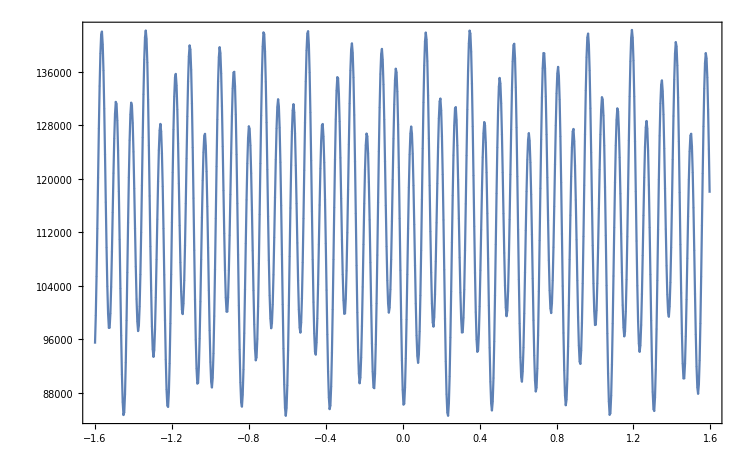

```mathematica
MyPlotfun[data, Frame -> True, Joined -> True]
```

Fast Fourier Transformation um Frequenzen auszulesen:

```mathematica
frdata = abskoef[data[[All, 2]], (data[[-1, 1]]-data[[1,1]])*801/800];
```

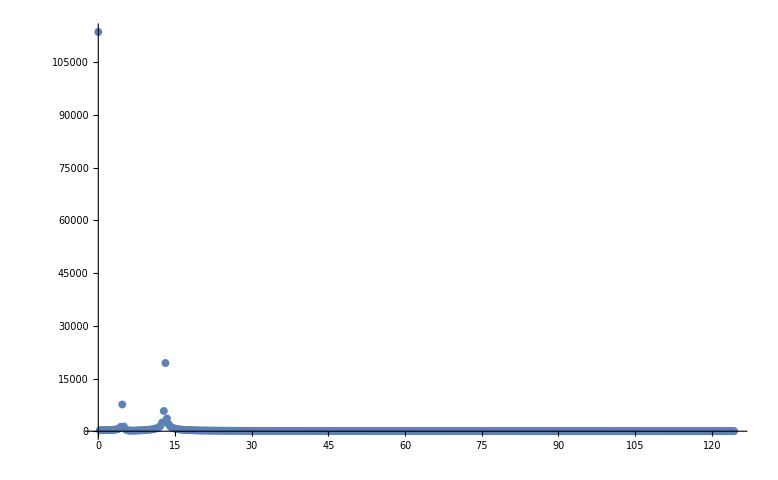

```mathematica
ListPlot[frdata, PlotRange -> All]
```

Drei Punkte: bei 0 (Offset, müssen wir rausnehmen), und zwei richtige Frequenzen

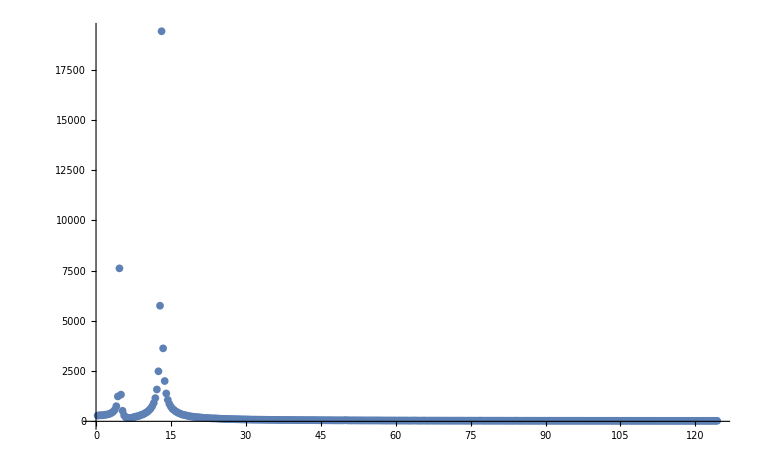

```mathematica
ListPlot[frdata[[2;;-1]], PlotRange -> All]
```